```mathematica
f[x_]:=Sin[x]-x/13
```

```mathematica
g[x_]:=x
h[x_] :=x/(1-x^2)
l[x_]:=x+0.5h[x]
l2[x_]:=x+2h[x]
l3[x_]:=x+4h[x]
l4[x_]:=x+10h[x]
l5[x_]:=x+20h[x]
```

```mathematica
NSolve[f[x]==0,x,Reals]
```

{{x→-8.69239},{x→-6.83698},{x→-2.91541},{x→0.},{x→2.91541},{x→6.83698},{x→8.69239}}

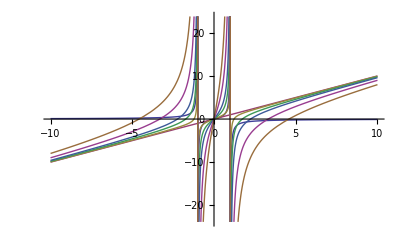

```mathematica
Plot[{h[x],g[x],l[x], l2[x], l3[x], l4[x], l5[x]},{x,-10,10}]
```

```mathematica
i[x_]:=x+1h[x]
```

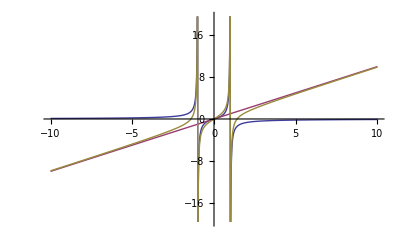

```mathematica
Plot[{h[x],g[x], i[x]},{x,-10,10}]
```

```mathematica
NSolve[h[x]==0,x,Reals]
```

{{x→0.}}

```mathematica
l[l[l[l[l[l[l[l[l[l[l[l[l[l[-10]]]]]]]]]]]]]]//N
```

-9.2675